```mathematica
(* Teardrop shape for use with magma chambers and blobs. *)
```

```mathematica
teardropFormula:={Cos[t]+Max[0,Cos[t]],Sin[t]*(1-Max[0,Cos[t]]^2)}
```

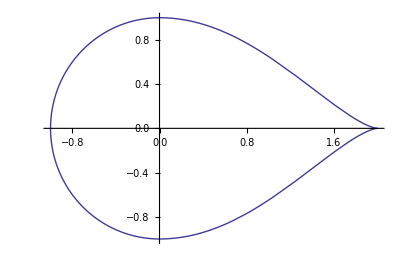

```mathematica
ParametricPlot[teardropFormula,{t,0,2*π}]
```

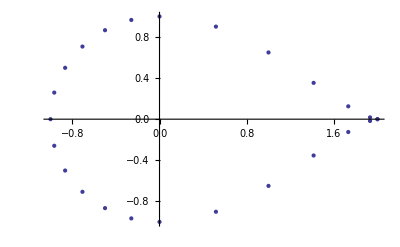

```mathematica
ListPlot[Table[teardropFormula,{t,0,2*π,π/12}]]
```

```mathematica
topFromTangent[v_]:={v[[2]],-v[[1]]}
```

```mathematica
bottomFromTangent[v_]:={-v[[2]],v[[1]]}
```

```mathematica
(* curvature for the subduction angle made up piecewise of lines and arcs *)
```

```mathematica
(* the ideal line is parametereized by t, with t0=0 being placed where the flat portion starts bending down *)
```

```mathematica
t0:=0
```

```mathematica
t1:=θ0*r0
```

```mathematica
t2:=t1+θ1*r1
```

```mathematica
t3:=t2+θ2*r2
```

```mathematica
(* c vectors are centers of the arcs that are there *)
```

```mathematica
c0:={d,y0-r0}
```

```mathematica
p0[t_]:= {d-t,y0}
```

```mathematica
pd0[t_]:={-1,0}
```

```mathematica
p1[t_]:=Module[{θ=π/2+(t-t0)/r0},c0+r0*{Cos[θ],Sin[θ]}]
```

```mathematica
pd1[t_]:=bottomFromTangent[Normalize[p1[t]-c0]]
```

```mathematica
c1:=p1[t1]+r1*Normalize[c0-p1[t1]]
```

```mathematica
p2[t_]:=Module[{θ=π/2+θ0+(t-t1)/r1},c1+r1*{Cos[θ],Sin[θ]}]
```

```mathematica
pd2[t_]:=bottomFromTangent[Normalize[p2[t]-c1]]
```

```mathematica
c2:=p2[t2]+r2*Normalize[c1-p2[t2]]
```

```mathematica
p3[t_]:=Module[{θ=π/2+θ0+θ1+(t-t2)/r2},c2+r2*{Cos[θ],Sin[θ]}]
```

```mathematica
pd3[t_]:=bottomFromTangent[Normalize[p3[t]-c2]]
```

```mathematica
dir4:=Module[{θ=θ0+θ1+θ2+π},{Cos[θ],Sin[θ]}]
```

```mathematica
p4[t_]:=p3[t3]+(t-t3)*dir4
```

```mathematica
pd4[t_]:=dir4
```

```mathematica
makeTop[f_,fd_,t_]:=f[t]+topFromTangent[fd[t]]*m
```

```mathematica
makeBottom[f_,fd_,t_]:=f[t]-topFromTangent[fd[t]]*m
```

```mathematica
makeCrustBottom[f_,fd_,t_]:=f[t]+topFromTangent[fd[t]]*cb
```

```mathematica
(* with actual values *)
```

```mathematica
crustTop:=-3000
```

```mathematica
crustThickness:=7000
```

```mathematica
lithoMantleThickness:=55000
```

```mathematica
lithosphereThickness:=crustThickness+lithoMantleThickness
```

```mathematica
totalAngle:=π/4
```

```mathematica
rules:={
d->40000,
y0->crustTop - lithosphereThickness/2, (* between top and bottom oceanic crust *)
m->lithosphereThickness/2,
cb->lithosphereThickness/2-crustThickness,
θ0->totalAngle*0.25,
r0->90000,
θ1->totalAngle*0.5,
r1->40000,
θ2->totalAngle*0.25,
r2->90000}
```

```mathematica
tright:=-400000
```

```mathematica
tleft:=t3+300000
```

```mathematica
xPadding:=(m/.rules)*1.2
```

```mathematica
xRange:={p4[tleft][[1]]-xPadding,p0[tright][[1]]+xPadding}/.rules
```

```mathematica
yPadding:=(m/.rules)*1.2
```

```mathematica
yRange:={p4[tleft][[2]]-yPadding,p0[tright][[2]]+yPadding}/.rules
```

```mathematica
segment[position_,derivative_,tStart_,tEnd_,color_]:={
(* middle line *)
ParametricPlot[position[t]/.rules,{t,tStart,tEnd},PlotStyle->{color,Dashed}],

(* top *)
ParametricPlot[makeTop[position,derivative,t]/.rules,{t,tStart,tEnd},PlotStyle->{color}],

(* bottom *)
ParametricPlot[makeBottom[position,derivative,t]/.rules,{t,tStart,tEnd},PlotStyle->{color}],

(* crust bottom *)
ParametricPlot[makeCrustBottom[position,derivative,t]/.rules,{t,tStart,tEnd},PlotStyle->{color}]
}
```

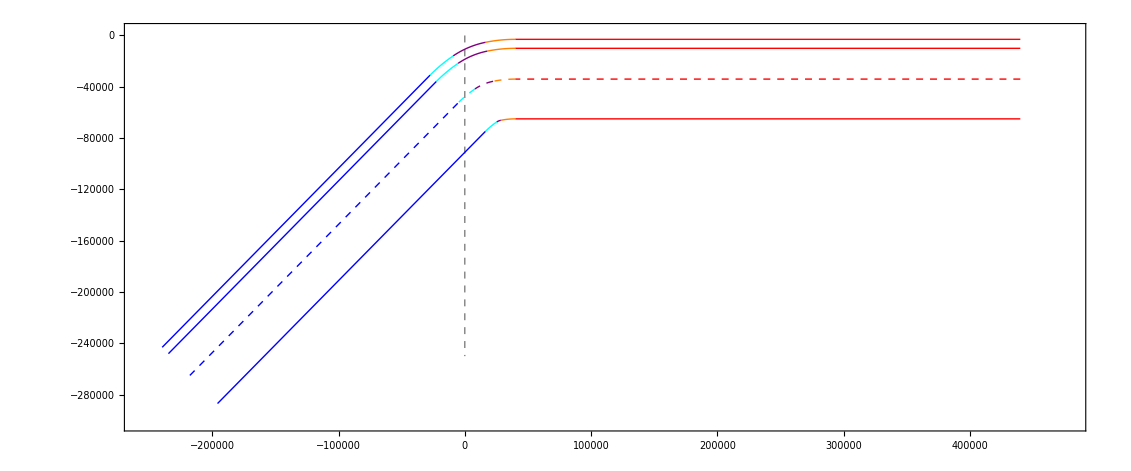

```mathematica
Show[
Flatten[{
Graphics[{Dashed,Gray,Line[{{0,0},{0,-250000}}]}],
segment[p0,pd0,tright,t0,Red],
segment[p1,pd1,t0,t1/.rules,Orange],
segment[p2,pd2,t1/.rules,t2/.rules,Purple],
segment[p3,pd3,t2/.rules,t3/.rules,Cyan],
segment[p4,pd4,t3/.rules,tleft/.rules,Blue]
}],
PlotRange->{xRange,yRange},Frame->True]
```

```mathematica
smokeFactor:=1 + Cos[20*t]/30
```

```mathematica
smokeFormula:={smokeFactor*Cos[t]+Max[0,Cos[t]],Sin[t]*(smokeFactor-Max[0,Cos[t]]^2)}
```

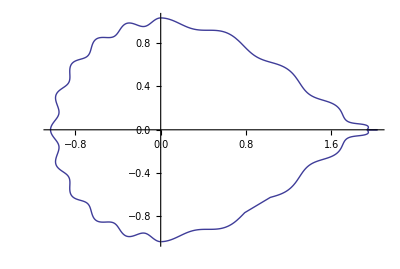

```mathematica
ParametricPlot[smokeFormula,{t,0,2*π}]
```